-1.38622/r^1.21524

NDSolve::precw: 参数函数的精度 ({{2. (-14.9998+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

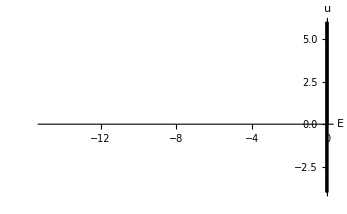

```mathematica
α=2.;u0=1.*10^-6;
V[r_]=-1.3862179318475605/r^1.2152447118079408
f[e_?NumberQ(*/;e∈Reals*)]:=
Block[{u,r,r1=1500.,r2=u0},
First[u[r2]/.
NDSolve[{u''[r]+(α(e-V[r])-0/r^2)u[r]==0,u[r1]==u0,u'[r1]==(*√(α(V[r1]-e)) u0*)-u0},
u,{r,r1,r2},Method->"Chasing",MaxSteps->Infinity,WorkingPrecision->20,MaxStepFraction->10^-3]]]
Plot[{f[e]},{e,-15,0},
(*PlotRange->{{-15,0},{-10,10}(*,{-10^-3,10^-3}*)},*)
AxesLabel->{"E","u"},
PlotStyle->Black,PlotPoints->100,PlotRange->{{-15,0},{-4,6}}]
```

```mathematica
FindRoot[f[e]==0,{e,5,1},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (5.+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (1.+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→1.}

```mathematica
FindRoot[f[e]==0,{e,0.016,0.015},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.016+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.015+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→0.0160595}

```mathematica
FindRoot[f[e]==0,{e,2,1},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (2.+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (1.+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (1.49427+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→1.57763}

```mathematica
FindRoot[f[e]==0,{e,0.22,0.175},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.22+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.175+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→0.325444}

```mathematica
FindRoot[f[e]==0,{e,1.4,1.3},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (1.4+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (1.3+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (1.35538+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→1.31401}

```mathematica
FindRoot[f[e]==0,{e,0.2,0.1},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.2+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.1+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→0.199926}

```mathematica
FindRoot[f[e]==0,{e,0.1,0.07},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.1+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.07+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.0891479+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-8,u'[1500.]==-1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→0.0702727}

```mathematica
FindRoot[f[e]==0,{e,0.08,0.07},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.08+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.07+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.0738949+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→0.0716513}

```mathematica
FindRoot[f[e]==0,{e,0.0013,0.0012},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0013+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.0012+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.00126082+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→0.00126957}

```mathematica
FindRoot[f[e]==0,{e,0.0054,0.0053},MaxIterations->1000]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0054+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.0053+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

NDSolve::precw: 参数函数的精度 ({{2. (0.00536137+1.38622 Power[«2»]) u[r]+u''[r]==0,u[1500.]==1.×10^-6,u'[1500.]==-1.×10^-6},{},{},{},{}}) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

{e→0.00536301}